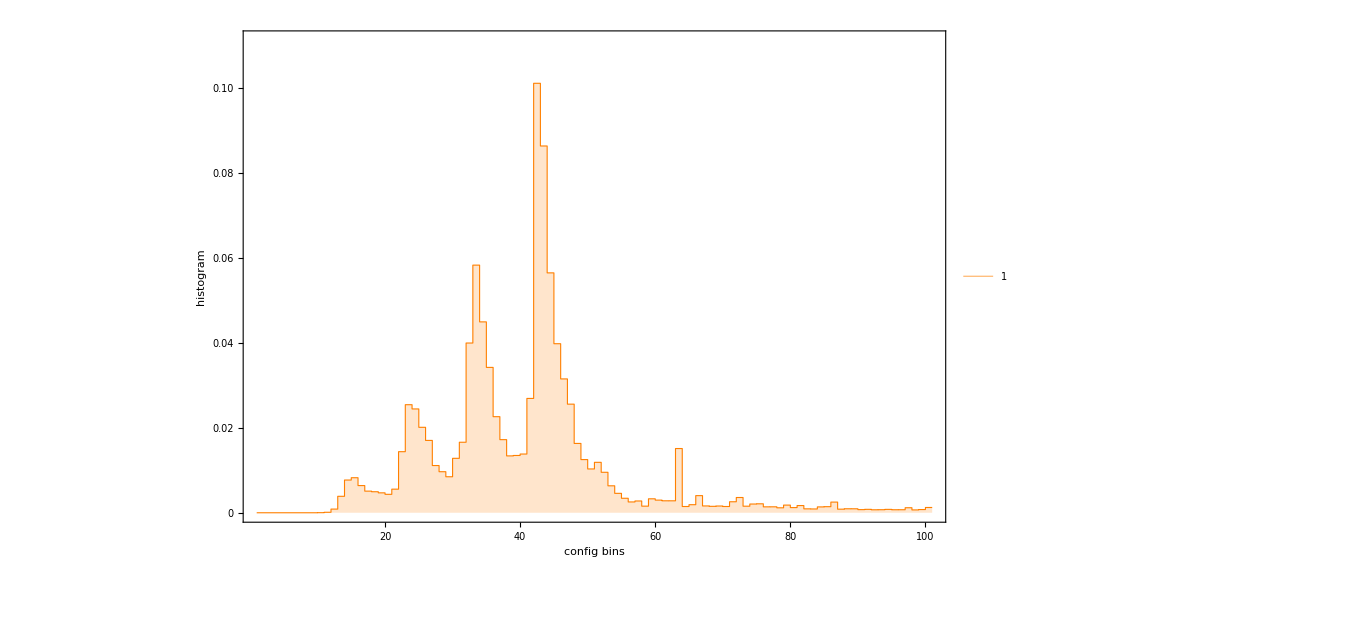

```mathematica
SetDirectory[NotebookDirectory[]];

D21=Import["dedf3/Hist-Plot-s-1.csv"];
D21sum=0.0;For[i=1,i<Length[D21]+1,i++,D21sum+=D21[[i]][[2]]];
For[i=1,i<Length[D21]+1,i++,D21[[i]][[2]]=D21[[i]][[2]]/D21sum];
D21Max=-10.0;For[i=1,i<Length[D21]+1,i++,D21Max=Max[D21Max,D21[[i]][[2]]]];
data={D21 }; 

tickFunc=Charting`ScaledTicks[{Identity,Identity},TicksLength->{.025,.015}][##]&;
markers1={
Graphics[Rectangle[],ImageSize->6],
Graphics[Rectangle[],ImageSize->6],
Graphics[Rectangle[],ImageSize->6]
};
style={
Directive[Orange,Thickness[0.0008]],
Directive[Blue,Thickness[0.0008]],  
Directive[Red,Thickness[0.0008]]
};

xlo=1.00;  xhi=101.00;
ylo=0.00;  yhi=1.1*Max[D21Max(*, D31Max,D41Max *)];
(** ListLogLinearPlot **)
ListStepPlot[
data,PlotStyle->style,Frame->True,Joined->True,Filling->Axis,PlotRange->{{xlo,xhi},{ylo,yhi}},ImageSize->1000,
FrameStyle->Directive[Black,28,Thick],FrameLabel->{"config bins","histogram"},FrameTicks->{{tickFunc,tickFunc},{tickFunc,tickFunc}},Filling->{4->{5}},
PlotLegends->Placed[LineLegend[Style[#,24,Bold]&/@{"1","31"(*,"41"*)},LegendFunction->"Frame"],{0.85,.85}]
]
```